```mathematica
f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
f2[x_]:=0.2*x
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
lstGrdLin={{-5,-3,3,5},{-1,-0.5,0.5,1}};
lstStyl1={{Blue,Thick},{Green,Thin,Dashed},{Red,Thin}};
lstStyl2={Directive[Thick,14],Directive[Thick,14]};
lstStyl3=Directive[Gray,Dotted];


rLgnd={"f1","f2","f3"};
Plot[{Sin[x^2],x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,3},ImageSize->540,PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,22]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],16,Plain,Blue,Background->LightYellow],PlotLegends->Placed[SwatchLegend[rLgnd,LegendLabel->"Легенда (типы и вид линий):",LegendLayout->"Row",LegendFunction->"Frame"],{{0.2,-0.01},{0.3,-0.8}}]]
```

-Graphics-

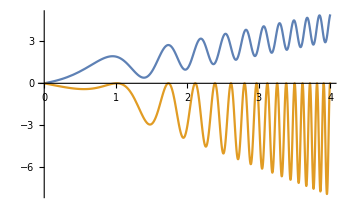
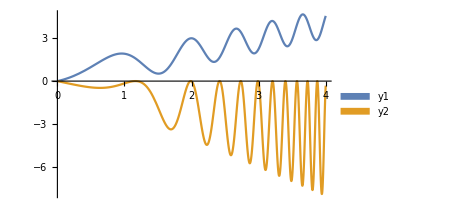

```mathematica
rLgnd={"y1","y2"};
pLgnd="Row";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
StringReplace["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"," "]
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ].

StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ]

```mathematica
StringLength[StringReplace[ToString["PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]"],Whitespace..:>""]]
```

52

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=c*d+(d*z^4)/(c+d)+d*z^2/(b+z)-(d+z)/(b+c*z^2)+(z*(c+a*z^2))/(d+z^3);
fRab
Numerator[fRab[[4]]]//InputForm
```

c d+(d z^4)/(c+d)+(d z^2)/(b+z)-(d+z)/(b+c z^2)+(z (c+a z^2))/(d+z^3)

-d - z

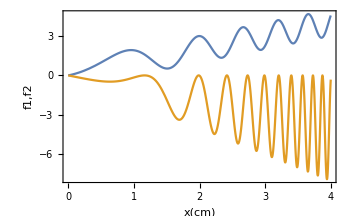
-Graphics--Graphics-

```mathematica
xFrmLbl="x(cm)";
yFrmLbl="f1,f2";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,Frame->True,FrameLabel->{xFrmLbl,yFrmLbl}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
lstR={1,4,73,9,-1,41,-7,-73,45,11,-2,40,3,-7,2,-5,11,5,41,8,42,73};
Select[lstR,x_/;Prime[x]&&x>10]
```

{}

```mathematica
bez = StringReplace[ToString["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"],Whitespace..:>""]
StringLength[bez]
```

],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2

50

```mathematica
"],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2"
```

```mathematica
r=48828125;t=1/11;
#^t&[r]
p=40353607;q=1/9;
#^q&[p]
```

5

7

```mathematica
t = RandomInteger[12,{10,5}]//MatrixForm
Cases[t,{x_,___,___,x_,___}]
```

(0 | 5 | 11 | 7 | 6
0 | 7 | 10 | 8 | 9
5 | 3 | 0 | 11 | 2
11 | 8 | 8 | 8 | 5
12 | 6 | 1 | 2 | 3
10 | 3 | 11 | 10 | 6
9 | 2 | 10 | 1 | 9
6 | 12 | 4 | 4 | 7
0 | 12 | 8 | 6 | 4
11 | 12 | 7 | 7 | 11)

{}

```mathematica
CellEvaluationDuplicate
```

```mathematica
bez = StringReplace[ToString["Filling→{1→{{4},{Yellow,Cyan}}}"],Whitespace..:>""]
StringLength[bez]
```

Filling→{1→{{4},{Yellow,Cyan}}}

31

```mathematica
lstR={1,4,32,9,-1,41,-7,-73,38,11,-2,40,3,-7,2,-5,11,5,41,8,42,73};
```

```mathematica
Select[lstR, x_/;EvenQ[x]&&x<41]
```

Select::normal: Nonatomic expression expected at position 1 in Select[lstR,x_/;EvenQ[x]&&x<41].

Select[lstR,x_/;EvenQ[x]&&x<41]

```mathematica
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[10*x^3];
grf1=Plot[x*f1[x]-x,{x,0.5,2.},PlotStyle->Purple];
grf2=Plot[x*f1[x]-x+0.5*f2[x],{x,0.5,2.},PlotStyle->Cyan];
grf3=Plot[x*f1[x]-x,{x,0.5,2.},PlotStyle->MeshShading];
grf4=Show[{grf1,grf2},PlotRange->{1,-5},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350];
grf5=Show[{grf2,grf3},PlotRange->{1,-5},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350];
Row[{grf4,grf5},Spacer[15]]
```

```mathematica
u=16777216;v=1/24;
#^v&[u]
```

2

```mathematica
FullSimplify[(35*(-((-(Sqrt[2]*3^(3/4))+2*Sqrt[3]*x)/(3-Sqrt[2]*3^(3/4)*x+Sqrt[3]*x^2))+(Sqrt[2]*3^(3/4)+2*Sqrt[3]*x)/(3+Sqrt[2]*3^(3/4)*x+Sqrt[3]*x^2)+(2*Sqrt[2])/(3^(1/4)*(1+(1-(Sqrt[2]*x)/3^(1/4))^2))+(2*Sqrt[2])/(3^(1/4)*(1+(1+(Sqrt[2]*x)/3^(1/4))^2))))/(28*Sqrt[2]*3^(3/4))]/.x->6/5//InputForm
```

3125/3171

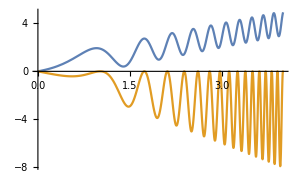
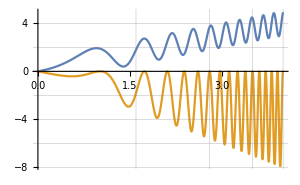

```mathematica
rClrTyp={Cyan,Dashed};
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300];
grf2=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300,GridLines->{{1.6,2.8,3.5,4}, {-8,-6,-4,-2,0,2,4}}];
Row[{grf1,grf2},Spacer[5]]
```

```mathematica
GridFrameMargins
```

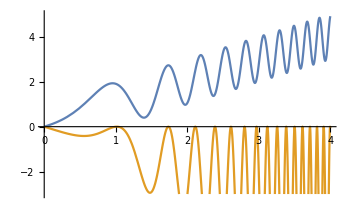
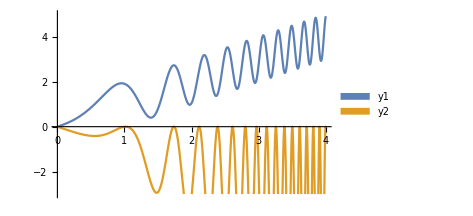

```mathematica
rLgnd={"y1","y2"};

grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350,PlotRange->{{0,4},{-3,5}}];
grf2=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350,PlotRange->{{0,4},{-3,5}},PlotLegends->Placed[SwatchLegend[rLgnd,LegendLayout->"Row"],{Left,Bottom}]];
Row[{grf1,grf2},Spacer[15]]
```

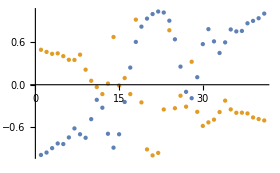
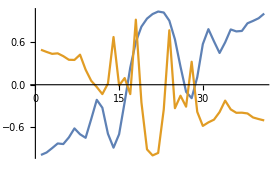

```mathematica
f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
f2[x_]:=0.2*x
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x

sData1=Table[f1[x],{x,-5,5,0.25}];
sData3=Table[f3[x],{x,-5,5,0.25}];
grSd1=ListPlot[{sData1,sData3},ImageSize->280];
grSd2=ListPlot[{sData1,sData3},ImageSize->280,Joined->True];
Row[{grSd1,grSd2},Spacer[5]]
```

```mathematica
IntegerReverse
```

```mathematica
rAB={10,18,7,14.,14,13,4 a,4,19.,16,1.,4 a,4 b,6/7,1,6,3,17.,8,8};
Cases[rAB,_Integer?(#<8&)]
```

{7,4,1,6,3}

```mathematica
Cond
```

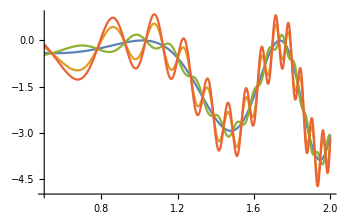
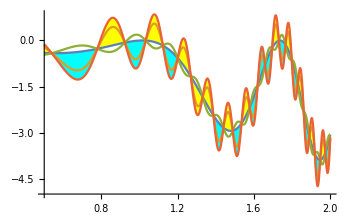

```mathematica
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[10*x^3];
grf1=Plot[{x*f1[x]-x,x*f1[x]-x+0.6*f2[x],x*f1[x]-x-0.2*f2[x],x*f1[x]-x+0.9*f2[x]},{x,0.5,2.},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350];
grf2=Plot[{x*f1[x]-x,x*f1[x]-x+0.6*f2[x],x*f1[x]-x-0.2*f2[x],x*f1[x]-x+0.9*f2[x]},{x,0.5,2.},BaseStyle->16,AxesOrigin->{0.5,-5},ImageSize->350,Filling->{1->{{4},{Yellow,Cyan}}}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
Region
```

```mathematica
CellLabelMargins
```

```mathematica
Manipulate[Plot[{Sin[a*x],Sin[a*x]+Sin[x]},{x,0,10},PlotStyle->{{Dotted,Green},Magenta},PlotRange->2.1,BaseStyle->22,AspectRatio->2/5,ImageSize->550],{a,1,5}]
```

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z^3+b*z^2-c/(d+z)+z/(d+z)+Cos[z];
Cases[fRab,_Denominator]
```

{}

```mathematica
aX="X";
aY="f1,f2";
f1[x_]:=Sin[1.5*x^3];
f2[x_]:=Cos[4*x^3];
grf1=Plot[{f1[x],f2[x]},{x,0,3/2},ImageSize->500,PlotL]
```

Plot[{f1[x],f2[x]},{x,0,3/2},ImageSize→500,PlotL]

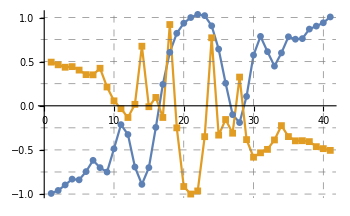
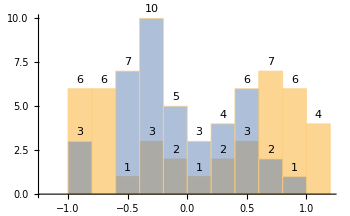

-Graphics--Graphics--Graphics-

```mathematica
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
sData3=Table[f3[x],{x,-5,5,0.25}];
grSdLPl1d=ListLinePlot[sData3,Joined->True,BaseStyle->14,Mesh->Full,AxesStyle->Directive[Black,Thick,14],GridLines->{{10,20,30,40},{-1,-0.75,-0.5,-0.25,0.25,0.5,0.75,1}},GridLinesStyle->Directive[Gray,Dashed],Filling->Axis,FillingStyle->LightRed,ImageSize->350];

f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
sData1=Table[f1[x],{x,-5,5,0.25}];

grSd1=ListPlot[{sData1,sData3},Joined->True,BaseStyle->14,AxesStyle->Directive[Black,Thick,14],GridLines->{{10,20,30,40},{-1,-0.75,-0.5,-0.25,0.25,0.5,0.75,1}},GridLinesStyle->Directive[Gray,Dashed],PlotMarkers->{Automatic,Small},ImageSize->350];
gr2Hst1=Histogram[{sData1,sData3},8,LabelingFunction->Above,ImageSize->350];

Row[{grSd1,gr2Hst1},Spacer[5]]

lstPieCh={2,4,8,4};

grPieCh1=PieChart[lstPieCh,ImageSize->220];
grPieCh2=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ImageSize->220];
grPieCh3=PieChart[lstPieCh,BaseStyle->14,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],ImageSize->220];

Row[{grPieCh1,grPieCh2,grPieCh3},Spacer[5]]
```

```mathematica
{{3,5,4,6,77,8,99}}//TableForm
```

3
5
4
6
77
8
99

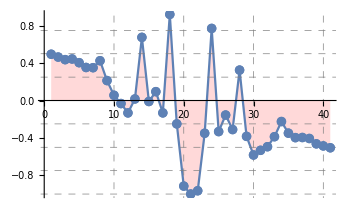
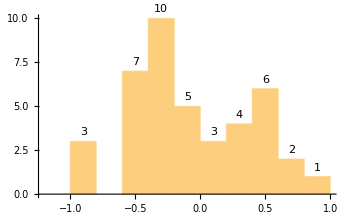

```mathematica
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x;
sData3=Table[f3[x],{x,-5,5,0.25}];
grSdLPl1d=ListLinePlot[sData3,Joined->True,BaseStyle->14,Mesh->Full,AxesStyle->Directive[Black,Thick,14],GridLines->{{10,20,30,40},{-1,-0.75,-0.5,-0.25,0.25,0.5,0.75,1}},GridLinesStyle->Directive[Gray, Dashed],Filling->Axis,FillingStyle->LightRed,ImageSize->350];
grHst1=Histogram[sData3,8,BaseStyle->14,LabelingFunction->Above,ImageSize->350];
Row[{grSdLPl1d,grHst1},Spacer[5]]
```

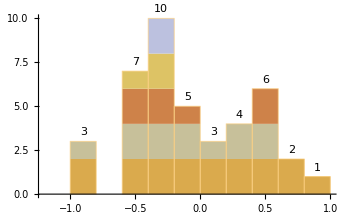
-Graphics--Graphics-

```mathematica
grHst2=Histogram[sData3,8,BaseStyle->14,LabelingFunction->Above,ChartElementFunction->"SegmentScaleRectangle",ImageSize->350];
Row[{grHst1,grHst2},Spacer[5]]
```

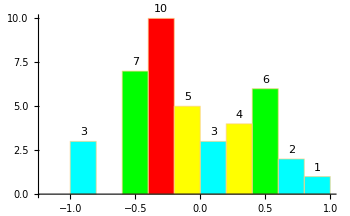
-Graphics--Graphics-

```mathematica
grHst3=Histogram[sData3,8,BaseStyle->14,LabelingFunction->Above,ColorFunction->(Which[#<4,Cyan,4≤#<6,Yellow,6≤#<9,Green,True,Red]&),ColorFunctionScaling->False,ImageSize->350];
Row[{grHst2,grHst3},Spacer[5]]
```

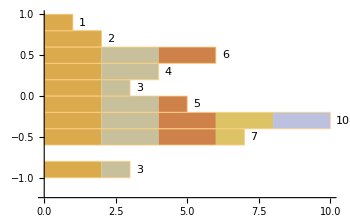
-Graphics--Graphics-

```mathematica
grHst4=Histogram[sData3,8,BaseStyle->14,ChartElementFunction->"SegmentScaleRectangle",LabelingFunction->After,BarOrigin->Left,ImageSize->350];
Row[{grHst2,grHst4},Spacer[5]]
```

```mathematica
grPHst1=PairedHistogram[sData1,sData3,8,BaseStyle->14,ImageSize->350];
grPHst2=PairedHistogram[sData1,sData3,8,BaseStyle->14,ColorFunction->(Which[#<4,Purple,4≤#<6,Orange,6≤#<9,Magenta,True,Brown]&),ColorFunctionScaling->False,ImageSize->350];
Row[{grPHst1,grPHst2},Spacer[5]]
```

-Graphics--Graphics-

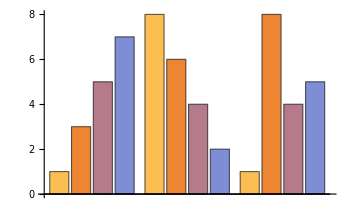
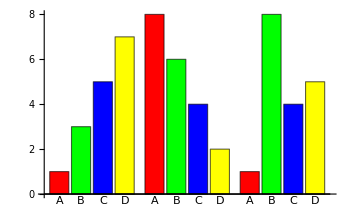

```mathematica
lst1={{1,3,5,7},{8,6,4,2},{1,8,4,5}};
grBrCh1=BarChart[lst1,BaseStyle->14,ImageSize->350];
grBrCh2=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},ImageSize->350];
Row[{grBrCh1,grBrCh2},Spacer[5]]
```

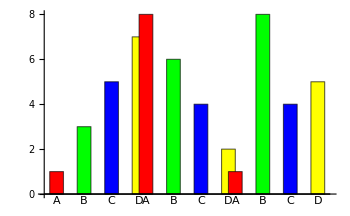
-Graphics--Graphics-

```mathematica
grBrCh3=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},BarSpacing->{1,-0.5},ImageSize->350];
Row[{grBrCh2,grBrCh3},Spacer[5]]
```

```mathematica
grBrCh4=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},BarSpacing->{1,-0.5},ChartBaseStyle->EdgeForm[Dashed],ImageSize->350];
Row[{grBrCh3,grBrCh4},Spacer[5]]
```

-Graphics--Graphics-

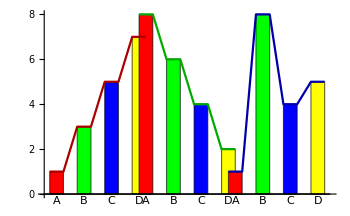
-Graphics--Graphics-

```mathematica
grBrCh5=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},BarSpacing->{1,-0.5},Joined->True,ImageSize->350];
Row[{grBrCh3,grBrCh5},Spacer[5]]
```

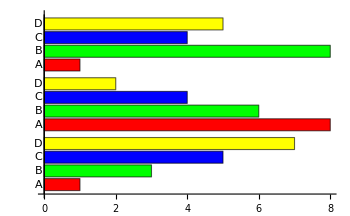
-Graphics--Graphics-

```mathematica
grBrCh6=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},BarOrigin->Left,ImageSize->350];
Row[{grBrCh2,grBrCh6},Spacer[5]]
```

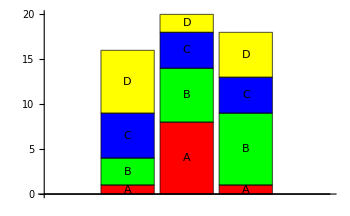
-Graphics--Graphics-

```mathematica
grBrCh7=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},ChartLayout->"Stacked",ImageSize->350];
Row[{grBrCh2,grBrCh7},Spacer[5]]
```

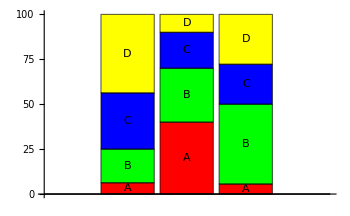
-Graphics--Graphics-

```mathematica
grBrCh8=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},ChartLayout->"Percentile",ImageSize->350];
Row[{grBrCh7,grBrCh8},Spacer[5]]
```

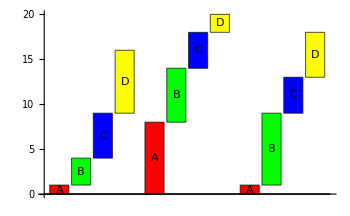
-Graphics--Graphics-

```mathematica
grBrCh9=BarChart[lst1,BaseStyle->14,ChartLabels->{"A","B","C","D"},ChartStyle->{Red,Green,Blue,Yellow},ChartLayout->"Stepped",ImageSize->350];
Row[{grBrCh2,grBrCh9},Spacer[5]]
```

```mathematica
lstPieCh={2,4,8,4};
grPieCh1=PieChart[lstPieCh,ImageSize->220];
grPieCh2=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ImageSize->220];
grPieCh3=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],ImageSize->220];
Row[{grPieCh1,grPieCh2,grPieCh3},Spacer[5]]
```

-Graphics--Graphics--Graphics-

```mathematica
grPieCh4=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],SectorOrigin->π/2,ImageSize->220];
grPieCh5=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],SectorOrigin->{Automatic,2/3},ImageSize->220];
Row[{grPieCh3,grPieCh4,grPieCh5},Spacer[5]]
```

-Graphics--Graphics--Graphics-

```mathematica
grPieCh6=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],SectorOrigin->{Automatic,2/3},ChartElementFunction->ChartElementDataFunction["GlassSector","GradientDirection"->"Radial"],ImageSize->220];
grPieCh7=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->Placed[lstPieCh,"RadialOuter"],SectorOrigin->{Automatic,2/3},ChartElementFunction->ChartElementDataFunction["GlassSector","GradientDirection"->"Angular"],ImageSize->220];
Row[{grPieCh3,grPieCh6,grPieCh7},Spacer[5]]
```

-Graphics--Graphics--Graphics-

```mathematica
grPieCh8=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},ChartLabels->{"s1","s2","s3","s4"},ImageSize->220];
grPieCh9=PieChart[lstPieCh,ChartStyle->{Red,Magenta,Green,Blue},LabelingFunction->"RadialCallout",ImageSize->220];
Row[{grPieCh3,grPieCh8,grPieCh9},Spacer[5]]
```

-Graphics--Graphics--Graphics-

40

"5^2,(5+1/6)^2,taranchuk,(5+2/6)^2,...,81"

```mathematica
(*Длина*)
StringLength[StringReplace[ToString["Denominator[Part[fRab,5]]"],Whitespace..:>""]]
StringReplace[ToString["Denominator[Part[fRab,5]]"],Whitespace..:>""]//InputForm
```

25

"Denominator[Part[fRab,5]]"

```mathematica
dCh={{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}};
dCh1={{4,2},{7,5},{4,3},{2,6},{7,5}};
dCh2={{2,3},{5,7},{4,3},{7,5},{4,3}};
grR1=PairedBarChart[dCh1,dCh2,PlotLabel->"gr1",ImageSize->350];
grR2=PairedBarChart[dCh,dCh2,BarOrigin->Left,PlotLabel->"gr2",ImageSize->350];
Row[{grR1,grR2},Spacer[10]]
```

PairedBarChart::ldata: {{{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}},{{2,3},{5,7},{4,3},{7,5},{4,3}}} is not a valid dataset or list of datasets.

General::stop: Further output of PairedBarChart::ldata will be suppressed during this calculation.

-Graphics-PairedBarChart[{{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}},{{2,3},{5,7},{4,3},{7,5},{4,3}},BarOrigin→Left,PlotLabel→gr2,ImageSize→350]

```mathematica
dCh={{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}};
grR1=BarChart[{{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}},PlotLabel->"gr1",ImageSize->350];
Show[grR1]
```

BarChart::ldata: {{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}} is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

Show::gtype: BarChart is not a type of graphics.

Show[BarChart[{{{2,3},{5,7},{4,3},{7,5},{4,3}},{{4,2},{7,5},{4,3},{2,6},{7,5}}},PlotLabel→gr1,ImageSize→350]]

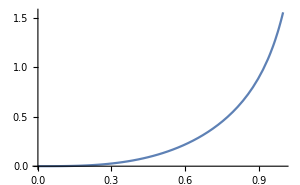
-Graphics--Graphics-

```mathematica
fnh[x_]:=Tan[x]
Row[{Plot[fnh[x^3],{x,0,1},ImageSize->300],Plot[fnh[x^3],{x,0,1},ImageSize->300]},Spacer[10]]
```

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z^3+b*z^2-c/(d+z)+z/(d+z)+Tan[z];
fRab[[3]]//InputForm
```

-(c/(d + z))

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=b*c+(c*z^4)/(a+b)+c*z^2/(c+z)+(z*(d+c*z^2))/(c+z^3)-(c+z)/(c+d*z^2);
fRab
Denominator[Part[fRab,5]]//InputForm
```

b c+(c z^4)/(a+b)+(c z^2)/(c+z)-(c+z)/(c+d z^2)+(z (d+c z^2))/(c+z^3)

c + z^3

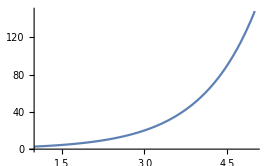
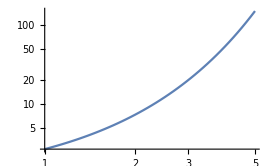

```mathematica
Row[{Plot[E^x,{x,1,5},ImageSize->270],LogLogPlot[E^x,{x,1,5},ImageSize->270]},Spacer[5]]
```

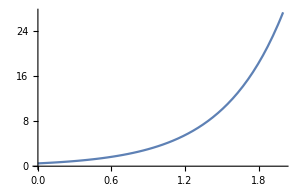
-Graphics-TanhPlot[ⅇ^(2 x)/2,{x,0,2},ImageSize→300]

```mathematica
fnh[x_]:=1/2*Exp[x]
Row[{Plot[fnh[2*x],{x,0,2},ImageSize->300],TanhPlot[fnh[2*x],{x,0,2},ImageSize->300]},Spacer[10]]
```

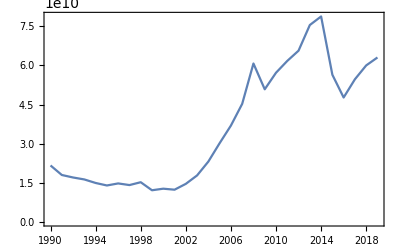

Belaruskij Dzjaržauny Universitet

```mathematica
DateListPlot[CountryData["Belarus",{"GDP",All}]]
(*GDP time series in current US dollars for each year*)


Interpreter["University"]["Belaruskij Dzjaržauny Universitet"](*Interpret universities*)
```

```mathematica
CountryData["Un*"]
```

{United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands}

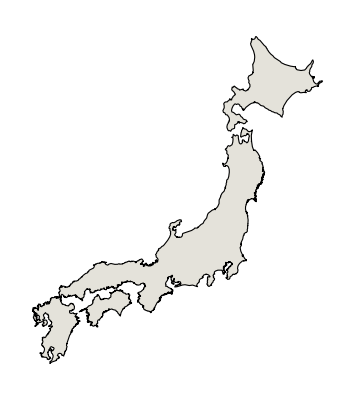

```mathematica
CountryData["Japan","Shape"]
```

```mathematica
UniversityData[Entity["University","BelaruskijDzjarzaunyUniversitet::4bp33"],"TuitionInternationalGradLocalCurrency"]
```

Missing[UnknownProperty,{University,TuitionInternationalGradLocalCurrency}]

```mathematica
BoxWhiskerChart
CandlestickChart
TradingChart
InteractiveTradingChart
```

```mathematica
RealDigits
```

```mathematica
dEPAMClose={{{2019,8,1},193.74},{{2019,8,2},187.83},{{2019,8,5},176.38},{{2019,8,6},179.91},{{2019,8,7},179.7},{{2019,8,8},189.98},{{2019,8,9},186.5},{{2019,8,12},186.56},{{2019,8,13},189.61},{{2019,8,14},182.34},{{2019,8,15},184.48},{{2019,8,16},188.02},{{2019,8,19},190.64},{{2019,8,20},193.27},{{2019,8,21},196.97},{{2019,8,22},195.5},{{2019,8,23},188.24},{{2019,8,26},188.97},{{2019,8,27},188.9},{{2019,8,28},189.75},{{2019,8,29},191.98},{{2019,8,30},191.33},{{2019,9,3},188.27},{{2019,9,4},191.44},{{2019,9,5},194.82},{{2019,9,6},192.89},{{2019,9,9},193.48},{{2019,9,10},176.13},{{2019,9,11},183.73},{{2019,9,12},184.17},{{2019,9,13},178.92},{{2019,9,16},180.95},{{2019,9,17},183.26},{{2019,9,18},184.56},{{2019,9,19},185.24},{{2019,9,20},185.79},{{2019,9,23},184.76},{{2019,9,24},181.78},{{2019,9,25},183.83},{{2019,9,26},183.64},{{2019,9,27},180.36},{{2019,9,30},182.32},{{2019,10,1},181.44},{{2019,10,2},180.02},{{2019,10,3},184.3},{{2019,10,4},188.91},{{2019,10,7},190.03},{{2019,10,8},184.51},{{2019,10,9},185.83},{{2019,10,10},184.44},{{2019,10,11},189.02},{{2019,10,14},188.2},{{2019,10,15},189.95},{{2019,10,16},188.45},{{2019,10,17},189.2},{{2019,10,18},186.96},{{2019,10,21},185.98},{{2019,10,22},170.},{{2019,10,23},171.85},{{2019,10,24},177.52},{{2019,10,25},176.15},{{2019,10,28},178.57},{{2019,10,29},176.62},{{2019,10,30},177.25}};
dEPAMClose=FinancialData["EPAM","Close",{{2019,08,1},{2019,10,30}}]
dEPAMClose={{{2019,8,1},193.74},{{2019,8,2},187.83},{{2019,8,5},176.38},{{2019,8,6},179.91},{{2019,8,7},179.7},{{2019,8,8},189.98},{{2019,8,9},186.5},{{2019,8,12},186.56},{{2019,8,13},189.61},{{2019,8,14},182.34},{{2019,8,15},184.48},{{2019,8,16},188.02},{{2019,8,19},190.64},{{2019,8,20},193.27},{{2019,8,21},196.97},{{2019,8,22},195.5},{{2019,8,23},188.24},{{2019,8,26},188.97},{{2019,8,27},188.9},{{2019,8,28},189.75},{{2019,8,29},191.98},{{2019,8,30},191.33},{{2019,9,3},188.27},{{2019,9,4},191.44},{{2019,9,5},194.82},{{2019,9,6},192.89},{{2019,9,9},193.48},{{2019,9,10},176.13},{{2019,9,11},183.73},{{2019,9,12},184.17},{{2019,9,13},178.92},{{2019,9,16},180.95},{{2019,9,17},183.26},{{2019,9,18},184.56},{{2019,9,19},185.24},{{2019,9,20},185.79},{{2019,9,23},184.76},{{2019,9,24},181.78},{{2019,9,25},183.83},{{2019,9,26},183.64},{{2019,9,27},180.36},{{2019,9,30},182.32},{{2019,10,1},181.44},{{2019,10,2},180.02},{{2019,10,3},184.3},{{2019,10,4},188.91},{{2019,10,7},190.03},{{2019,10,8},184.51},{{2019,10,9},185.83},{{2019,10,10},184.44},{{2019,10,11},189.02},{{2019,10,14},188.2},{{2019,10,15},189.95},{{2019,10,16},188.45},{{2019,10,17},189.2},{{2019,10,18},186.96},{{2019,10,21},185.98},{{2019,10,22},170.},{{2019,10,23},171.85},{{2019,10,24},177.52},{{2019,10,25},176.15},{{2019,10,28},178.57},{{2019,10,29},176.62},{{2019,10,30},177.25}};
CandlestickChart[dEPAMClose,BaseStyle->14,AspectRatio->4/10,ImageSize->500]
```

TimeSeries[…]

CandlestickChart::ldata: {{{2019,8,1},193.74},{{2019,8,2},187.83},{{2019,8,5},176.38},{{2019,8,6},179.91},{{2019,8,7},179.7},{{2019,8,8},189.98},{{2019,8,9},186.5},{{2019,8,12},186.56},«35»,{{2019,10,2},180.02},{{2019,10,3},184.3},{{2019,10,4},188.91},{{2019,10,7},190.03},{{2019,10,8},184.51},{{2019,10,9},185.83},{{2019,10,10},184.44},«14»} is not a valid dataset or list of datasets.

General::stop: Further output of CandlestickChart::ldata will be suppressed during this calculation.

CandlestickChart[{{{2019,8,1},193.74},{{2019,8,2},187.83},{{2019,8,5},176.38},{{2019,8,6},179.91},{{2019,8,7},179.7},{{2019,8,8},189.98},{{2019,8,9},186.5},{{2019,8,12},186.56},{{2019,8,13},189.61},{{2019,8,14},182.34},{{2019,8,15},184.48},{{2019,8,16},188.02},{{2019,8,19},190.64},{{2019,8,20},193.27},{{2019,8,21},196.97},{{2019,8,22},195.5},{{2019,8,23},188.24},{{2019,8,26},188.97},{{2019,8,27},188.9},{{2019,8,28},189.75},{{2019,8,29},191.98},{{2019,8,30},191.33},{{2019,9,3},188.27},{{2019,9,4},191.44},{{2019,9,5},194.82},{{2019,9,6},192.89},{{2019,9,9},193.48},{{2019,9,10},176.13},{{2019,9,11},183.73},{{2019,9,12},184.17},{{2019,9,13},178.92},{{2019,9,16},180.95},{{2019,9,17},183.26},{{2019,9,18},184.56},{{2019,9,19},185.24},{{2019,9,20},185.79},{{2019,9,23},184.76},{{2019,9,24},181.78},{{2019,9,25},183.83},{{2019,9,26},183.64},{{2019,9,27},180.36},{{2019,9,30},182.32},{{2019,10,1},181.44},{{2019,10,2},180.02},{{2019,10,3},184.3},{{2019,10,4},188.91},{{2019,10,7},190.03},{{2019,10,8},184.51},{{2019,10,9},185.83},{{2019,10,10},184.44},{{2019,10,11},189.02},{{2019,10,14},188.2},{{2019,10,15},189.95},{{2019,10,16},188.45},{{2019,10,17},189.2},{{2019,10,18},186.96},{{2019,10,21},185.98},{{2019,10,22},170.},{{2019,10,23},171.85},{{2019,10,24},177.52},{{2019,10,25},176.15},{{2019,10,28},178.57},{{2019,10,29},176.62},{{2019,10,30},177.25}},BaseStyle→14,AspectRatio→2/5,ImageSize→500]

```mathematica
ScaleRanges
```

```mathematica
Array[#^2+#^3&,7,5]//InputForm
```

{150, 252, 392, 576, 810, 1100, 1452}

```mathematica
IntegerLength
```

```mathematica
PolarAxes
```

```mathematica
StringCases
```

```mathematica
Count[cMatr2,u_/;Sin[u]<0.8]
```

0

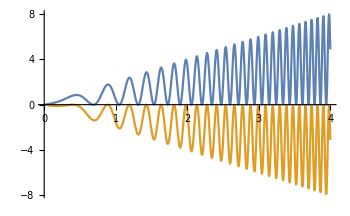
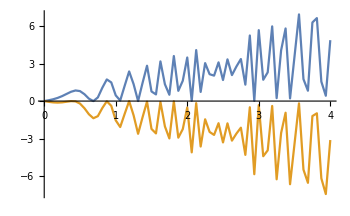

```mathematica
grf1=Plot[{x+x*Sin[10*x^2],x*Sin[10*x^2]-x},{x,0,4},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+x*Sin[10*x^2],x*Sin[10*x^2]-x},{x,0,4},BaseStyle->18,ImageSize->350,PlotPoints->2];
Row[{grf1,grf2},Spacer[15]]
```

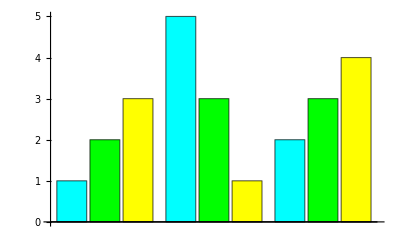
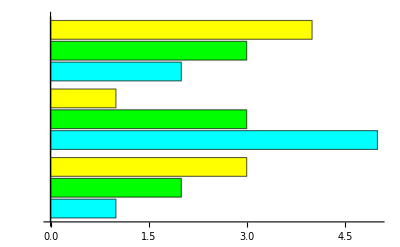

```mathematica
dataBarChart={{1,2,3},{5,3,1},{2,3,4}};
grBarCh1=BarChart[dataBarChart,ChartStyle->{Cyan,Green,Yellow},ImageSize->400];
grBarCh2=BarChart[dataBarChart,ChartStyle->{Cyan,Green,Yellow},BarOrigin->Left,ImageSize->400];
Row[{grBarCh1,grBarCh2},Spacer[10]]
```

```mathematica
Solve[E^(-1/4*a)-E^(-1/4*b)==0.25,{a,b}]
```

$Aborted

```mathematica
Solve[24*p*(4-p)==6*(4-p)+6*p*(4-p)+3*p^2*(4-p)+p^3*(4-p)+p^4/4,p]
```

{{p→Root-6.84Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,1]-6.839027823306795},{p→Root0.357Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,2]0.35719149974817543},{p→Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084},{p→Root5.38Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,4]5.380583820183345}}

```mathematica
Root"2.43"Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084
```

Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084

```mathematica
Solve[24*p*(4-p)-(6*(4-p)+6*p*(4-p)+3*p^2*(4-p)+p^3*(4-p)+p^4/4)==0,p]
```

{{p→Root-6.84Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,1]-6.839027823306795},{p→Root0.357Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,2]0.35719149974817543},{p→Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084},{p→Root5.38Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,4]5.380583820183345}}

```mathematica
24*p*(4-p)-(6*(4-p)+6*p*(4-p)+3*p^2*(4-p)+p^3*(4-p)+p^4/4)/.p->2.43
```

0.194976

```mathematica
Root[-96+312#1-120#1^2-4#1^3+3#1^4&,3]
```

Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084

```mathematica
Solve[-96+312*x-120*x^2-4*x^3+3*x^4==0,x][[3]]
```

{x→Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084}

```mathematica
Solve[24*p*(4-p)-(6*(4-p)+6*p*(4-p)+3*p^2*(4-p)+p^3*(4-p)+p^4/4)==0,p]
N[%]
```

{{p→Root-6.84Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,1]-6.839027823306795},{p→Root0.357Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,2]0.35719149974817543},{p→Root2.43Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,3]2.4345858367086084},{p→Root5.38Root[-96+312 #1-120 #1^2-4 #1^3+3 #1^4&,4]5.380583820183345}}

{{p→-6.83903},{p→0.357191},{p→2.43459},{p→5.38058}}

```mathematica
Solve[(1+p+p^2/2+p^3/6+p^4/24)^(-1)*p==0.25,p]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→-3.3363-4.22787 ⅈ},{p→-3.3363+4.22787 ⅈ},{p→0.357383},{p→2.31522}}

```mathematica
Solve[1/4*p^4+p^3+3*p^2-18*p+6==0,p]
N[%]
```

{{p→Root0.357Root[24-72 #1+12 #1^2+4 #1^3+#1^4&,1]0.3573828691454033},{p→Root2.32Root[24-72 #1+12 #1^2+4 #1^3+#1^4&,2]2.3152213437086675},{p→Root-3.34-4.23 ⅈRoot[24-72 #1+12 #1^2+4 #1^3+#1^4&,3]-3.3363021064270355},{p→Root-3.34+4.23 ⅈRoot[24-72 #1+12 #1^2+4 #1^3+#1^4&,4]-3.3363021064270355}}

{{p→0.357383},{p→2.31522},{p→-3.3363-4.22787 ⅈ},{p→-3.3363+4.22787 ⅈ}}

```mathematica
(1+p+p^2/2+p^3/6+p^4/24)^(-1)/.p->0.36
```

0.697702

```mathematica
Solve[0.25*t*E^(-0.25*t)==0.25,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→1.42961},{t→8.61317}}

```mathematica
0.25*t*E^(-0.25*t)/.t->1.42961
```

0.25